# QSP phase gates: rotation angles for the qubit-controlled displacement circuit

This notebook compiles a phase gate exp(-i f(x)) on the oscillator position x into a sequence of qubit rotations interleaved with qubit-controlled displacements, using quantum signal processing (QSP). It is the compiler that produced the rotation angles run in the experiment for all five gates in the paper.

The steps are:

1. Expand exp(-i f(x)) in M+1 Fourier harmonics on the interval -2 <= x <= 2. Writing w = Exp[-I beta x], this gives a degree-M polynomial P(w) with coefficients co.

2. Find a complementary polynomial Q(w) such that |P|^2 + |Q|^2 = 1 for all |w| = 1, by numerical minimisation over the coefficients of Q.

3. Peel P and Q apart one layer at a time to get one rotation (theta, phi, lambda) per layer, and convert these angles to the echoed-conditional-displacement (ECD) convention used on hardware.

4. Rebuild the circuit from the angles and compare its P-block with the target.

The notebook is set up for the Morse gate. For the other gates change f and order in the first input cell; everything downstream is unchanged. Targets and orders used in the paper (f is the phase V(x) programmed by the gate):

cubic: f = 0.6 x^3, order = 11

symmetric double well: f = 0.1 x^4 - 0.3 x^2, order = 12

asymmetric double well: f = 0.1 x^4 - 0.3 x^2 + 0.1 x, order = 14

broken double well: f = 0.1 x^4 - 0.3 x^2 + 0.6 x, order = 13

Morse: f = 0.6 (1 - Exp[-0.8 (x + 0.5)])^2, order = 13

The multistart in Section 2 uses random seeds, so a rerun gives a Q (and hence angles) that can differ slightly from the stored outputs. The angles actually run are the stored outputs of Section 3 and are also listed in the Python operator-error notebook.

## 1. Target phase and its Fourier coefficients

xrange sets the Fourier interval -xrange <= x <= xrange, and beta = Pi/xrange is the displacement step, so w = Exp[-I beta x] is periodic on that interval. Here xrange = 2 and beta = Pi/2. order is the polynomial degree M (M+1 harmonics). f is the target phase.

co[[n+1]] is the n-th Fourier coefficient of exp(-i f(x)), computed by numerical integration over the interval. The extra factor Exp[-I order beta x/2] shifts the harmonics from -M/2..M/2 to 0..M so that they form an ordinary polynomial in w. exp is the resulting truncated series; it is the best the circuit can do at this order.

```mathematica
xrange=2;
β=π/xrange;(*range of x with good accuracy*)
order= 13;(*order of polynomial*)
f=0.6(1-Exp[-0.8(x+0.5)])^2;(*set the potential*)
co=Table[NIntegrate[Exp[-I f]  Exp[-I order β x/2]Exp[I n β x],{x,-π/β,π/β}]/(2π/β),{n,0,order}]//Chop;
exp=Sum[co⟦n+1⟧Exp[-I n β x],{n,0,order}];
```

## 2. Complementary polynomial Q

A QSP circuit implements a 2x2 unitary whose top-left element is P(w). Unitarity requires a partner Q(w) of the same degree with |P(w)|^2 + |Q(w)|^2 = 1 on the unit circle. Writing the coefficients of Q as b_n = r_n Exp[I Pi xi_n] (r_n >= 0, -1 <= xi_n <= 1), the cell below multiplies out 1 - P P* - Q Q*, collects its coefficient of each power of w, and sums their squared magnitudes into the cost Expression1. The cost is zero exactly when Q is complementary.

The commented-out block at the end of this cell is an earlier single-start minimisation (NMinimize followed by repeated FindMinimum). It is kept for reference and is not executed.

```mathematica
PPstar=Sum[co⟦n+1⟧w^n,{n,0,order}]*Sum[Conjugate[co⟦n+1⟧] w^-n,{n,0,order}];
QQstar=Sum[(ToExpression["r"<>ToString[n+1]]*Exp[I ToExpression["ξ"<>ToString[n+1]]π])w^n,{n,0,order}]*Sum[(ToExpression["r"<>ToString[n+1]]*Exp[-I ToExpression["ξ"<>ToString[n+1]]π])w^-n,{n,0,order}]//Expand;(*set up the expression of |Q|^2*)
var=Flatten[Table[{ToExpression["r"<>ToString[n+1]], ToExpression["ξ"<>ToString[n+1]]},{n,0,order}]];
(*Here bn=rn*Exp[I*ξn*π]*)
s=(1-PPstar-QQstar)*w^order//Expand;
ss=CoefficientList[s,w];
Expression1=Sum[((ComplexExpand[Re[ss]])^2+(ComplexExpand[Im[ss]])^2)⟦n⟧,{n,1,Dimensions[ss]⟦1⟧}];(*set up the array contains Coefficient[1-|P(w)|^2-|Q(w)|^2,w^n], and then minimize the length of that array to determine the coefficents*)
 (*sol1=NMinimize[Expression1,var];(*Determine bn=rn*Exp[I*ξn*π] by minimization*)
minvar=Flatten[Table[{{ToExpression["r"<>ToString[n]],Last[sol1⟦2⟧⟦2n-1⟧]},{ToExpression["ξ"<>ToString[n]],Last[sol1⟦2⟧⟦2n⟧]}},{n,1,Dimensions[var]⟦1⟧/2}]];
minvar2=Table[{minvar⟦2n-1⟧,minvar⟦2n⟧},{n,1,Dimensions[var]⟦1⟧}];
sol2=FindMinimum[Expression1,minvar2];
Table[minvar=Flatten[Table[{{ToExpression["r"<>ToString[n]],Last[sol2⟦2⟧⟦2n-1⟧]},{ToExpression["ξ"<>ToString[n]],Last[sol2⟦2⟧⟦2n⟧]}},{n,1,Dimensions[var]⟦1⟧/2}]];
minvar2=Table[{minvar⟦2n-1⟧,minvar⟦2n⟧},{n,1,Dimensions[var]⟦1⟧}];
sol2=FindMinimum[Expression1,minvar2],{n,1,30}]; *)
```

Multistart minimisation: 50 local minimisations (interior point, up to 1500 iterations) from random seeds r_n in [0, 1], xi_n in [-1, 1]. The runs are sorted by cost and the best one is stored in sol2 = {cost, {r1 -> ..., xi1 -> ..., ...}}, which the rest of the notebook reads. A residual cost of order 1e-3 is typical; the circuit is unitary regardless, and the remaining mismatch shows up as a small difference between the compiled and target operator, which the paper accounts for by comparing every measurement with the compiled circuit.

```mathematica
(* ==========================================*)(*MULTISTART OPTIMIZATION FOR Q(w) VARIABLES*)(* ==========================================*)numStarts=50;
allResults={}; (*Initialize an empty list to store all runs*)

Monitor[Do[(*1. Generate random seeds for r_n and ξ_n*)randomSeeds=Flatten[Table[{{ToExpression["r"<>ToString[n]],RandomReal[{0,1}]},{ToExpression["ξ"<>ToString[n]],RandomReal[{-1,1}]}},{n,1,order+1}],1];
(*2. Run the local optimizer*)Quiet[currentRun=FindMinimum[Expression1,randomSeeds,MaxIterations->1500,Method->"InteriorPoint"]];
(*3. Store the result in our master list*)(*Format of currentRun is {cost,{r1->val,ξ1->val,...}}*)AppendTo[allResults,currentRun];,{start,1,numStarts}],Row[{"Running seed: ",start,"/",numStarts}]];

(*4. Sort all results by their cost function (lowest cost first)*)
allResults=SortBy[allResults,First];

(*5. Set'sol2' to the absolute best result so the rest of your script still works smoothly*)
sol2=allResults[[1]];
bestCost=sol2[[1]];

Print["Optimization Complete!"];
Print["Total seeds evaluated: ",Length[allResults]];
Print["Best Cost Found: ",bestCost];
```

Optimization Complete!

Total seeds evaluated: 50

Best Cost Found: 0.00148081

## 3. Rotation angles

RR[theta, phi, lambda] is the single-qubit rotation used for each layer. matrixProduct multiplies a list of matrices in order.

```mathematica
RR[θ_,ϕ_,λ_]:=({{Exp[I λ+I ϕ]Cos[θ], Exp[I ϕ]Sin[θ]}, {Exp[I λ]Sin[θ], -Cos[θ]}})(*Define the rotation matrix*)
matrixProduct[listOfMatrices_]:=Dot@@listOfMatrices
(*Define the function to calculate the product of matrices from a list*)
```

Layer stripping. Starting from P and Q, each step reads off the highest-order coefficients a1 (of P) and b1 (of Q), sets theta = ArcTan[|b1|/|a1|] and phi = Arg[a1/b1], and applies the inverse rotation, which lowers the degree of both polynomials by one. After M steps the remainder is a constant, whose phase gives the final lambda. angPra lists the angles in stripping order; angCD reverses them into circuit (time) order, with lambda on the first rotation. The last three lines rebuild the circuit from these angles, alternating rotations with the controlled displacement diag(w, 1), and keep its top-left element as Pfinal.

### Note on a factor of Pi in the next cell (as-run convention)

The optimisation above parameterises the coefficients of Q as b_n = r_n Exp[I Pi xi_n]. The first line of the next cell, which rebuilds Q for the angle extraction (cq), uses Exp[I xi_n] instead, without the factor Pi. The angles stored in this notebook, and the angles run in the experiment for every gate, come from that line exactly as written.

What the factor does. With Pi, cq is the complementary polynomial found by the optimisation, and the extracted circuit reproduces P, the Fourier-truncated gate of Section 1, up to the small residual cost of the optimisation. Without Pi, every phase of Q is scaled down by Pi, so Q is no longer exactly complementary to P. Every layer of the circuit is still a unitary rotation and the layer stripping still returns a valid circuit, but its top-left element (Pfinal, plotted in Section 4) is a slightly different order-M approximation of the target. Writing Exp[I Pi Last[...]] in cq gives the alternative angle set.

How large the difference is. The operator-error notebook (07_operator_errors.ipynb) compares the as-run circuit with the Fourier-truncated gate, which the with-Pi circuit closely reproduces (SM, Compiled-circuit errors). Over the analysis windows of the paper (cubic |x| <= 1.8, double wells |x| <= 1.5, Morse |x| <= 1.6), relative to the with-Pi angles, the as-run angles:

have a smaller amplitude error (rms of 1 - A_M about half as large, e.g. cubic 0.017 vs 0.041, Morse 0.029 vs 0.058), since the compiled gate is a matrix element of a unitary;

have a larger phase error (rms up to 2-3 times larger, e.g. cubic 0.048 vs 0.025 rad, Morse 0.072 vs 0.028 rad), concentrated near the window edges;

have essentially the same rms operator error |K_g - exp(-iV)| (0.015-0.076 vs 0.015-0.064), with a larger worst point (fidelity bound up to 3.5e-2 vs below 1e-2);

keep the acceptance A_M^2 above 0.8 in every window, as the with-Pi angles do.

Why it does not change the claims. The paper never compares the data with the ideal target alone: every comparison (Sim, the force curves, the acceptance, the fits and the operator-error budget) is made against the compiled operator rebuilt from the angles actually run, Pfinal here and K_g in the Python notebooks. The measured forces agree with that circuit, and both angle sets approximate the target potentials to the same overall accuracy. Including Pi would mainly trade a smaller phase error near the window edges for a larger amplitude error.

```mathematica
(* As run: the phase below is Exp[I xi_n], without the factor Pi used in the optimisation (b_n = r_n Exp[I Pi xi_n]). Writing Exp[I Pi Last[...]] gives the alternative angle set discussed in the text above. *)
cq=Table[Last[sol2⟦2⟧⟦2n-1⟧]Exp[I Last[sol2⟦2⟧⟦2n⟧]],{n,1,Dimensions[var]⟦1⟧/2}];
Pd=Sum[co⟦n+1⟧w^n,{n,0,order}]//N//Expand;
Qd=Sum[cq⟦n+1⟧w^n,{n,0,order}]//N//Expand;
dim=Dimensions[var]⟦1⟧/2;
angPra=Table[{a1=Coefficient[Pd*w^dim,w^(dim+order-(n-1))];
b1=Coefficient[Qd*w^dim,w^(dim+order-(n-1))];
θd=ArcTan[Abs[b1]/Abs[a1]];
ϕd=Arg[a1/b1];
PdN=Exp[-I ϕd]Cos[θd]Pd/w+Sin[θd]Qd/w//Expand//Chop;
QdN=Exp[-I ϕd]Sin[θd]Pd-Cos[θd]Qd//Expand//Chop;
Pd=PdN;
Qd=QdN;
θd,
ϕd,
If[n==dim-1,Arg[Coefficient[Qd*w^dim,w^dim]],0]},{n,1,dim}](*there are three parameters of each rotation Rd, they are θd, ϕd and λd*);
angCD=Table[{angPra⟦Dimensions[angPra]⟦1⟧-n⟧⟦1⟧,angPra⟦Dimensions[angPra]⟦1⟧-n⟧⟦2⟧,If[n==0,angPra⟦Dimensions[angPra]⟦1⟧-n-1⟧⟦3⟧,0]},{n,0,Dimensions[angPra]⟦1⟧-1}];
listofmatrix=Table[RR[angPra⟦n⟧⟦1⟧,angPra⟦n⟧⟦2⟧,0].({{w, 0}, {0, 1}})//N,{n,1,order}];
finalmatrix=matrixProduct[listofmatrix].RR[angPra⟦order+1⟧⟦1⟧,angPra⟦order+1⟧⟦2⟧,angPra⟦order⟧⟦3⟧];
Pfinal=finalmatrix⟦1⟧⟦1⟧/.{w->Exp[-I x β]}//Expand;
```

### Angles in the conditional-displacement (CD) convention

One row {theta, phi, lambda} per rotation, in the order they are applied. Only the first rotation carries a nonzero lambda.

```mathematica
angCD
```

{{0.415542,-0.0485164,-2.95614},{0.365583,0.276982,0},{0.341532,0.796983,0},{0.383634,0.47799,0},{0.531426,0.586181,0},{0.546921,0.64375,0},{0.644149,-3.0586,0},{1.34279,-0.508319,0},{0.41978,-0.0968862,0},{0.280762,0.23565,0},{0.239002,-0.0140294,0},{0.275197,-0.270027,0},{0.272174,2.76984,0},{1.39723,0.268603,0}}

### Angles in the ECD convention (as run on hardware)

The hardware uses echoed conditional displacements, which also flip the qubit: U_ECD = e^{i beta x}|e><g| + e^{-i beta x}|g><e|. Absorbing the flip into the rotations gives theta -> Pi/2 - theta, phi -> phi - Pi and lambda -> -lambda for every rotation after the first (angles taken mod 2 Pi); the first rotation is unchanged. angECD is the list uploaded to the experiment.

```mathematica
(*when we consider Subscript[U, ECD]=e^iβx|e><g|+e^-iβx|g><e|*)
(*The mappings are θd -> π/2-θd, ϕd -> ϕd-π and λd->-λd for d=2,3...,N+1 and no change for d=1*)
```

```mathematica
angECD=Join[{{angCD⟦1⟧⟦1⟧,angCD⟦1⟧⟦2⟧,angCD⟦1⟧⟦3⟧}},Table[{Mod[π/2-angCD⟦n⟧⟦1⟧,2π],Mod[angCD⟦n⟧⟦2⟧-π,2π],-angCD⟦n⟧⟦3⟧},{n,2,Dimensions[angCD]⟦1⟧}]];
angECD
```

{{0.415542,-0.0485164,-2.95614},{1.20521,3.41858,0},{1.22926,3.93858,0},{1.18716,3.61958,0},{1.03937,3.72777,0},{1.02387,3.78534,0},{0.926648,0.0829967,0},{0.228004,2.63327,0},{1.15102,3.04471,0},{1.29003,3.37724,0},{1.33179,3.12756,0},{1.2956,2.87157,0},{1.29862,5.91143,0},{0.173567,3.4102,0}}

The Fourier coefficients of the target, for reference.

```mathematica
co
```

{-0.0312841-0.0270312 ⅈ,0.0391606+0.0433095 ⅈ,-0.0450818-0.0728529 ⅈ,0.0381266+0.125177 ⅈ,0.0139943-0.208266 ⅈ,-0.190374+0.296467 ⅈ,0.634439-0.270548 ⅈ,0.560757+0.0175185 ⅈ,-0.0580301+0.0385946 ⅈ,0.0360298-0.0298468 ⅈ,-0.0224983+0.0202678 ⅈ,0.0151388-0.0153064 ⅈ,-0.0108484+0.0122443 ⅈ,0.00812347-0.0101644 ⅈ}

## 4. Check against the target

Real and imaginary parts of the ideal exp(-i f) against the compiled P-block (Pfinal, multiplied by Exp[I order beta x/2] to undo the harmonic shift of Section 1), and the potential recovered from the compiled phase, -Im Log[...], against f. Agreement is expected across -2 <= x <= 2, with the largest deviations near the interval edges.

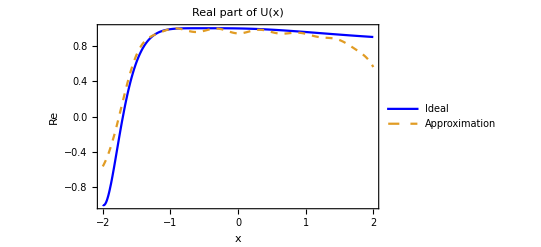

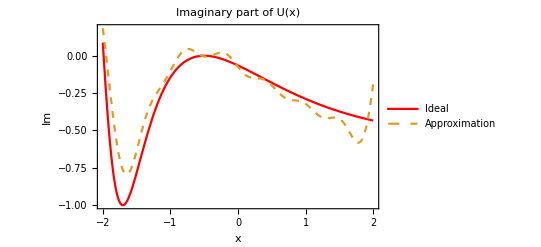

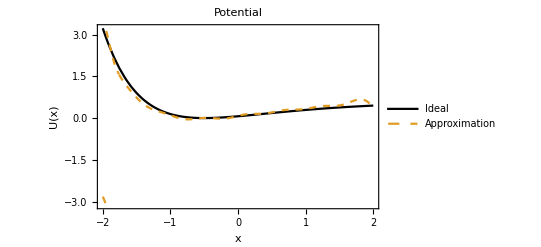

```mathematica
Plot[{Re[Exp[-I f]],Re[Pfinal Exp[I order β x/2]]},{x,-π/β,π/β},PlotRange->All,PlotLabel->"Real part of U(x)",PlotLegends->{"Ideal","Approximation"},PlotStyle->{Blue,Dashed},Frame->True,FrameLabel->{"x","Re"},Axes->False]
Plot[{Im[Exp[-I f]],Im[Pfinal Exp[I order β x/2]]},{x,-π/β,π/β},PlotRange->All,PlotLabel->"Imaginary part of U(x)",PlotLegends->{"Ideal","Approximation"},PlotStyle->{Red,Dashed},Frame->True,FrameLabel->{"x","Im"},Axes->False]
Plot[{f,-Im[Log[Pfinal Exp[I order β x/2]]]},{x,-π/β,π/β},PlotRange->All,PlotLabel->"Potential",PlotLegends->{"Ideal","Approximation"},PlotStyle->{Black,Dashed,Dashed,Dashed},Frame->True,FrameLabel->{"x","U(x)"},Axes->False]
```